# MS-C1650 - Numerical Analysis Week 17: Lecture 4: Interpolation - Different Bases

## Harri Hakula, 2021

## Reference

Let us define a reference set of points for our interpolation examples.

(19 x)/12+(77 x^2)/24-(25 x^3)/12+(7 x^4)/24

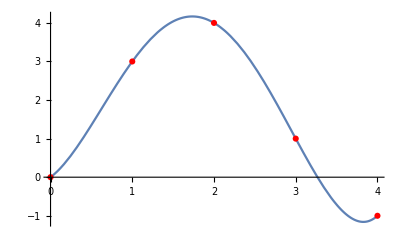

```mathematica
data={{0,0},{1,3},{2,4},{3,1},{4,-1}};
ip=Expand@InterpolatingPolynomial[data,x]
Show[Plot[ip,{x,0,4}],ListPlot[data,PlotStyle->Red,PlotMarkers->Automatic]]
```

## Lagrange

```mathematica
Clear@LagrangeShapes
```

```mathematica
LagrangeShapes[data_]:=Block[{x,len,ind,local},
len=Length[data];
ind=Range[len];
Table[
Product[(x-data[[j,1]])/(data[[i,1]]-data[[j,1]]),{j,Complement[ind,{i}]}]
,{i,len}]
]
```

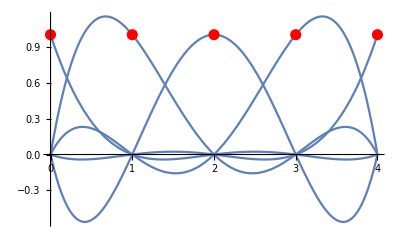

```mathematica
Plot[LagrangeShapes[data],{x,0,4},Epilog->{Red,PointSize[0.02],Point@Thread[List[Range[0,4],1]]}]
```

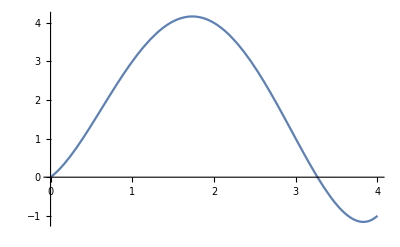

```mathematica
Plot[data[[All,2]].LagrangeShapes[data],{x,0,4}]
```

```mathematica
Show[Plot[data[[All,2]].LagrangeShapes[data],{x,0,4}],ListPlot[data,PlotStyle->Red,PlotMarkers->Automatic]]
```

-Graphics-

```mathematica
lp=Expand[data[[All,2]].LagrangeShapes[data]]
```

(19 x)/12+(77 x^2)/24-(25 x^3)/12+(7 x^4)/24

```mathematica
lp-ip
```

0

## Newton

```mathematica
NewtonCoefficients[data_]:=Block[{L,b,n,x,a},
n=Length[data];
x=data[[All,1]];
b=data[[All,2]];
L=ConstantArray[0,{n,n}];
L[[All,1]]=1;
Do[
L[[j;;,j]]=Product[x[[j;;]]-x[[k]],{k,1,j-1}]
,{j,2,n}];
a=LinearSolve[L,b];
a
]
```

```mathematica
NewtonBasis[data_]:=Block[{n,x,shapes},
n=Length[data];
shapes=Table[Product[x-data[[j,1]],{j,1,k}],{k,1,n-1}];
Prepend[shapes,1]
]
```

```mathematica
a=NewtonCoefficients[data]
```

{0,3,-1,-1/3,7/24}

```mathematica
shapes=NewtonBasis[data]
```

{1,x,(-1+x) x,(-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x}

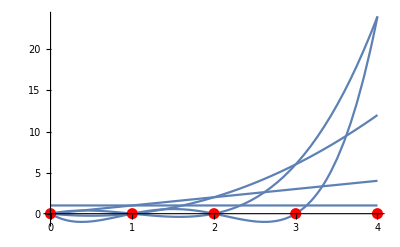

```mathematica
Plot[NewtonBasis[data],{x,0,4},Epilog->{Red,PointSize[0.02],Point@Thread[List[Range[0,4],0]]},PlotRange->All]
```

```mathematica
np=Expand[a.shapes]
```

(19 x)/12+(77 x^2)/24-(25 x^3)/12+(7 x^4)/24

```mathematica
np-ip
```

0

## Divided Differences

Divided differences are important both in theoretical and low-level practical applications. Here we define them using recursion.

```mathematica
Clear@DividedDifference
```

```mathematica
DividedDifference[{{x_?NumericQ,y_?NumericQ}}]:=y
```

```mathematica
DividedDifference[data:{{_?NumericQ,_?NumericQ}..}]/;Length[data]>1:=(DividedDifference[Rest[data]]-DividedDifference[Most[data]])/(data[[-1,1]]-data[[1,1]])
```

```mathematica
data
```

{{0,0},{1,3},{2,4},{3,1},{4,-1}}

```mathematica
Table[DividedDifference[data[[1;;k]]],{k,Length[data]}]
```

{0,3,-1,-1/3,7/24}

```mathematica
NewtonCoefficients[data]
```

{0,3,-1,-1/3,7/24}